```mathematica
(* -------- Test set on subset of coords and no burn in, no fitness cost ---------*)
SetDirectory["~/Dropbox/SpatialModelRepo/Runs"];
```

```mathematica
<<"../Alphas";

dli=Table[0.005 5^i,{i,-1,2,.5}];
xli=Range[0,0.8,0.1];

numpatli={9401,4483,9401};
tab={};
```

```mathematica
Do[input={"../InputData/C_Set_24_"<>ToString[rep]<>"_disp"<>ToString[dd]<>".txt","../InputData/C_Set_12_"<>ToString[rep]<>"_disp"<>ToString[dd]<>".txt","../InputData/C_Set_12B_"<>ToString[rep]<>"_disp"<>ToString[dd]<>".txt"}[[size]];


pa=Flatten[{numruns=1,maxT=29 365(*must not exceed 10585*),NumPat=numpatli[[size]],muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=xli[[xx]],eA=0.95,drivertime=25 365+150,NumDriver=50000,NumDriverPat=1,d=dli[[dd]],Ld=5/110.,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0li[[size,dd]],al0var=0.,al1li[[size,dd]] ,amp=0,resp=1,recstart=10,recend=maxT,recIntGlob=1,recIntLoc=1,recsitesfreq=1,set=10000size+1000 xx+100dd+rep-1,"e","r",start=23 365+1,input,"../InputData/RainDailyAvAv.csv","../InputData/Rellist.csv","../InputData/gamb_mortality_Aug25.csv",outputtype=3}];
If[rep==1,AppendTo[tab,{set,{"24","12","12B"}[[size]],xli[[xx]],dli[[dd]]}]];
(*If[i==1,Print[set/100]];*)
Export["./PP"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{size,3},{rep,1},{xx,Length[xli]},{dd,Length[dli]}];
```

```mathematica
Length[dli]
```

7

```mathematica
(* -------- Now set runs for animation---------*)
Do[input={"../InputData/C_Set_24_"<>ToString[rep]<>"_disp"<>ToString[dd]<>".txt","../InputData/C_Set_12_"<>ToString[rep]<>"_disp"<>ToString[dd]<>".txt","../InputData/C_Set_12B_0_"<>ToString[rep]<>"_disp"<>ToString[dd]<>".txt"}[[size]];


pa=Flatten[{numruns=1,maxT=29 365(*must not exceed 10585*),NumPat=numpatli[[size]],muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=xli[[xx]],eA=0.95,drivertime=25 365+150,NumDriver=50000,NumDriverPat=1,d=dli[[dd]],Ld=5/110.,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0li[[size,dd]],al0var=0.,al1li[[size,dd]] ,amp=0,resp=1,recstart=10,recend=maxT,recIntGlob=1,recIntLoc=10,recsitesfreq=1,set=100000+10000size+1000 xx+100dd+rep-1,"e","r",start=23 365+1,input,"../InputData/RainDailyAvAv.csv","Rellist.csv","../InputData/gamb_mortality_Jan25.csv",outputtype=-1}];
If[rep==1,AppendTo[tab,{set,{"24","12","12B"}[[size]],xli[[xx]],dli[[dd]]}]];
(*If[i==1,Print[set/100]];*)
Export["./PP"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{size,1},{rep,1},{xx,{1,3,5,7,9}},{dd,{1,3,5,7}}];
```

```mathematica
tab=PrependTo[tab,{"index", "trial size","fitness cost","dispersal rate"}];
MatrixForm[tab[[1;;5]]]
Length[tab]
Export["ParameterTableFull.csv",tab,"CSV","TextDelimiters"->""];
```

(index | trial size | fitness cost | dispersal rate
11100 | 24 | 0. | 0.001
11200 | 24 | 0. | 0.00223607
11300 | 24 | 0. | 0.005
11400 | 24 | 0. | 0.0111803)

190

```mathematica
Dimensions[tab]
```

{189,4}

```mathematica
Directory[]
```

/home/ace/Dropbox/FieldTrials/CRT/CRTModel/R1KC

```mathematica
(* -------- Now set WT runs ---------*)
setli={};
Do[
input={"../InputData/C_Set_24_0_disp"<>ToString[dd]<>".txt","../InputData/C_Set_12_0_disp"<>ToString[dd]<>".txt","../InputData/C_Set_12B_0_disp"<>ToString[dd]<>".txt"}[[size]];
pa=Flatten[{numruns,maxT,numpatli[[size]],muJ,muA,beta,theta,meanTL,mindev,gamma,xiA,eA,drivertime=25 365+150,NumDriver=0,NumDriverPat,d=dli[[dd]],Ld,psi,muAES,thide1,thide2,twake1,twake2,al0li[[size,dd]],al0var,al1li[[size,dd]],amp,resp,recstart,recend,recIntGlob,recIntLoc,recsitesfreq,set=100 size+dd,"e","r",start,input,"../InputData/RainDailyAvAv.csv","Rellist.csv","../InputData/gamb_mortality_Jan25.csv",outputtype=3}];
Export["./PPWT"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""];
AppendTo[setli,set],{i,1},{xx,1},{dd,Length[dli]},{size,3}];
```

```mathematica
setli
```

{101,201,301,102,202,302,103,203,303,104,204,304,105,205,305,106,206,306,107,207,307}

```mathematica
Do[
input={"../InputData/C_Set_24_"<>ToString[i]<>".txt","../InputData/C_Set_12_"<>ToString[i]<>".txt","../InputData/C_Set_half_12_"<>ToString[i]<>".txt"}[[size]];
pa=Flatten[{numruns,maxT,numpatli[[size]],muJ,muA,beta,theta,meanTL,mindev,gamma,xiA,eA,drivertime=25 365+150,NumDriver=0,NumDriverPat,d=dli[[dd]],Ld,psi,muAES,thide1,thide2,twake1,twake2,al0,al0var,al1 ,amp,resp,recstart=5 365,recend,recIntGlob,recIntLoc,recsitesfreq,set=1000000+100 size+dd,"e","r",start=27 365+1,input,"../InputData/RainDailyAvAv.csv","Rellist.csv","../InputData/gamb_mortality_Jan25.csv",outputtype=-1}];
Export["./PPWT"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{i,1},{xx,1},{dd,Length[dli]},{size,3}];
```

```mathematica
buildInHou=1.5987024553412008*^6;
PeopleInHou=1688410;(*The most recent estimate for the population of Houet Province,Burkina Faso,is approximately 1,688,410 as of 2023. This figure comes from data provided by Burkina Faso Open Data,which tracks population statistics by province*)
MosPerPerson=22.4; (*peak season estiamte from malaria prevalence*)
(**)
cooHalf=Import["../InputData/C_Set_24_"<>ToString[1]<>".txt","Table"];
buildHalf=Total[cooHalf[[All,3]]];
cooQuarter=Import["../InputData/C_Set_12_"<>ToString[1]<>".txt","Table"];
buildQuart=Total[cooQuarter[[All,3]]];         
mosAll=MosPerPerson (PeopleInHou/buildInHou){buildHalf,buildQuart,buildHalf}
```

{3.78582×10^7,9.12618×10^6,3.78582×10^7}

```mathematica
size=1;dd=1;
correc=Table[0,{i,3},{d,Length[dli]}];
```

```mathematica
Do[
WTloc=Partition[Drop[Import["./output_files/LocalData"<>ToString[1000000+100size+dd]<>"run1.txt","Table"],2],numpatli[[size]]];tot=N[Max[Table[Total[WTloc[[time,All,4]]],{time,366,730,1}]]];
correc[[size,dd]]=mosAll[[size]]/tot;
Print[{dd,size,correc[[size,dd]]}],{size,{3}},{dd,Length[dli]}];
```

{1,3,0.138561}

{2,3,0.138628}

{3,3,0.138869}

{4,3,0.139455}

{5,3,0.141102}

{6,3,0.145057}

{7,3,0.153676}

```mathematica
Do[

input={"../../InputData/C_Set_24_"<>ToString[i]<>".txt","../../InputData/C_Set_12_"<>ToString[i]<>".txt","../../InputData/C_Set_half_12_"<>ToString[i]<>".txt"}[[size]];
pa=Flatten[{numruns=1,maxT=29 365(*must not exceed 10585*),NumPat=numpatli[[size]],muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=xli[[xx]],eA=0.95,drivertime=25 365+150,NumDriver=50000,NumDriverPat=1,d=dli[[dd]],Ld=5/110.,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0 correc[[size,dd]],al0var=0.,al1 correc[[size,dd]],amp=0,resp=1,recstart=10,recend=maxT,recIntGlob=1,recIntLoc=1,recsitesfreq=1,set=10000size+1000 xx+100dd+i-1,"e","r",start=23 365+1,input,"../../InputData/RainDailyAvAv.csv","Rellist.csv","../../InputData/gamb_mortality_Jan25.csv",outputtype=3}];
If[i==1,AppendTo[tab,{set,{24,12,12}[[size]],xli[[xx]],dli[[dd]]}]];
(*If[i==1,Print[set/100]];*)
Export["./PP"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{size,3},{i,100},{xx,Length[xli]},{dd,Length[dli]}];
```

```mathematica
9 7 3 100
```

18900

```mathematica
correc
```

{{0.141118,0.141188,0.141389,0.142045,0.143741,0.147806,0.156547},{0.140087,0.14023,0.140588,0.141612,0.144059,0.149848,0.162393},{0.138561,0.138628,0.138869,0.139455,0.141102,0.145057,0.153676}}

```mathematica
2190/365
```

6

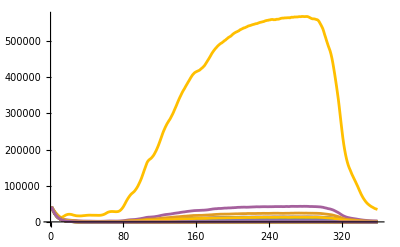

```mathematica
ListLinePlot[Table[WTloc[[All,i,4]],{i,24}],PlotRange->All]
```

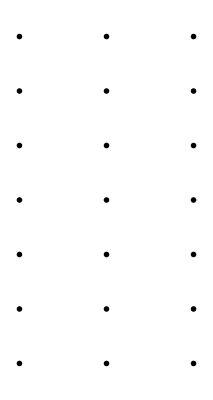

```mathematica
GraphicsGrid[Table[Plot[x,{x,0,10}],{j,7},{i,3}]]
```